```mathematica
ClearAll["Global`*"]
```

```mathematica
y = {10.0787617156523,-9.51866467444093,9.73922587306449,11.5662681883816,9.62798489000074,-9.60265090119919,8.90114345923455,10.866328444034,10.5347883361026,8.60577222463504,-10.625227428575,-9.08615131315038,-8.99280046532217,9.43533905966944,8.92696803962787,9.642301288006,9.42066621557773,9.90838406119759,9.63911912487384,7.55585122379505,9.58069898235901,9.63228461457187,-9.99589804304319,8.61024296515084,-10.4988882191036,-8.45028703711596,9.76066425342707,-8.68129886943495,9.83763492226261,7.29698608457303,8.78881675784227,10.6057117460834,10.2807363791435,9.54352982843898,-10.9911972452721,12.2061931600758,7.76887153466896,10.7523541087606,-9.98525551020183,10.6248182699128}
```

{10.0788,-9.51866,9.73923,11.5663,9.62798,-9.60265,8.90114,10.8663,10.5348,8.60577,-10.6252,-9.08615,-8.9928,9.43534,8.92697,9.6423,9.42067,9.90838,9.63912,7.55585,9.5807,9.63228,-9.9959,8.61024,-10.4989,-8.45029,9.76066,-8.6813,9.83763,7.29699,8.78882,10.6057,10.2807,9.54353,-10.9912,12.2062,7.76887,10.7524,-9.98526,10.6248}

```mathematica
epslist = N[Range[-0.5,0.5,(0.5-(-0.5))/40]]
```

{-0.5,-0.475,-0.45,-0.425,-0.4,-0.375,-0.35,-0.325,-0.3,-0.275,-0.25,-0.225,-0.2,-0.175,-0.15,-0.125,-0.1,-0.075,-0.05,-0.025,0.,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5}

```mathematica
thetaRange = Range[0,1,0.2]
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
mu0Range = Range[-12,-8,0.1]
```

{-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.}

```mathematica
mu1Range = Range[5,15,5]
```

{5,10,15}

```mathematica
ptheta[theta_]:=1
```

```mathematica
pmu0[mu0_,eps_]:=PDF[NormalDistribution[-10,1+eps], mu0]
```

```mathematica
pmu1[mu1_]:=PDF[NormalDistribution[10,1],mu1]
```

```mathematica
pu[theta_, mu0_, mu1_, eps_]:=ptheta[theta]*pmu0[mu0,eps]*pmu1[mu1]
```

```mathematica
L[theta_, mu0_, mu1_, y_]:=theta *PDF[NormalDistribution[mu0,1],y]+(1-theta)*PDF[NormalDistribution[mu1,1],y]
```

```mathematica
Ltable = Table[L[theta, mu0, mu1, y[[i]]],{i, 1, Length[y]}]
```

{(ⅇ^(-1/2 (10.0788-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.0788-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.51866-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.51866-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.73923-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.73923-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (11.5663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (11.5663-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.62798-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.62798-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.60265-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.60265-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.90114-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.90114-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.8663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.8663-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.5348-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.5348-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.60577-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.60577-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-10.6252-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.6252-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.08615-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.08615-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-8.9928-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.9928-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.43534-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.43534-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.92697-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.92697-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.6423-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.6423-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.42067-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.42067-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.90838-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.90838-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.63912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63912-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (7.55585-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.55585-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.5807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.5807-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.63228-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63228-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.9959-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.9959-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.61024-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.61024-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-10.4989-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.4989-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-8.45029-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.45029-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.76066-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.76066-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-8.6813-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.6813-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.83763-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.83763-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (7.29699-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.29699-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.78882-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.78882-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.6057-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6057-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.2807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.2807-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.54353-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.54353-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-10.9912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.9912-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (12.2062-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (12.2062-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (7.76887-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.76887-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.7524-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.7524-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.98526-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.98526-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.6248-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6248-mu0)^2) theta)/(√(2 π))}

```mathematica
Ltable[[1]]
```

(ⅇ^(-1/2 (10.0788-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.0788-mu0)^2) theta)/(√(2 π))

```mathematica
Ltotal[theta_, mu0_, mu1_]=(Times@@Ltable)
```

((ⅇ^(-1/2 (-10.9912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.9912-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-10.6252-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.6252-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-10.4989-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.4989-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.9959-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.9959-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.98526-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.98526-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.60265-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.60265-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.51866-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.51866-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.08615-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.08615-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-8.9928-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.9928-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-8.6813-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.6813-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-8.45029-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.45029-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (7.29699-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.29699-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (7.55585-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.55585-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (7.76887-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.76887-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.60577-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.60577-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.61024-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.61024-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.78882-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.78882-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.90114-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.90114-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.92697-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.92697-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.42067-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.42067-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.43534-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.43534-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.54353-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.54353-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.5807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.5807-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.62798-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.62798-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.63228-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63228-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.63912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63912-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.6423-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.6423-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.73923-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.73923-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.76066-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.76066-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.83763-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.83763-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.90838-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.90838-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.0788-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.0788-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.2807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.2807-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.5348-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.5348-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.6057-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6057-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.6248-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6248-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.7524-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.7524-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.8663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.8663-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (11.5663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (11.5663-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (12.2062-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (12.2062-mu0)^2) theta)/(√(2 π)))

```mathematica
Ltotal[theta=0.3,mu0=-13,mu1=10]
```

5.89653×10^-63

```mathematica
(*Plot3D[Ltotal[0.3,mu0, mu1], {mu0, -12,-8},{mu1, 8,12}, PlotRange->Full]*)
```

```mathematica
(*Plot3D[pu[theta=0.3,mu0,mu1,eps=0], {mu0, -12,-8},{mu1, 8,12}, PlotRange->Full]*)
```

```mathematica
plu[theta_, mu0_, mu1_, eps_]:=pu[theta, mu0, mu1, eps] * Ltotal[theta, mu0, mu1]
```

```mathematica
(*Plot3D[plulog[0.3,mu0,mu1,eps=0], {mu0, -15,-5},{mu1, 5,15}, PlotRange->Full]*)
```

```mathematica
{time,mu0Table} = Timing[Table[NIntegrate[plu[theta, mu0, mu1,0], {theta,0,1}, {mu1,5,15}],{mu0, mu0Range}]]
```

{7.13419,{1.94039×10^-51,2.87908×10^-50,3.78881×10^-49,4.42219×10^-48,4.5778×10^-47,4.20301×10^-46,3.42255×10^-45,2.47185×10^-44,1.58336×10^-43,8.99544×10^-43,4.53263×10^-42,2.02564×10^-41,8.02894×10^-41,2.82253×10^-40,8.80045×10^-40,2.43364×10^-39,5.96885×10^-39,1.29841×10^-38,2.50504×10^-38,4.28651×10^-38,6.50546×10^-38,8.75661×10^-38,1.04539×10^-37,1.1069×10^-37,1.03949×10^-37,8.65798×10^-38,6.39585×10^-38,4.19049×10^-38,2.43509×10^-38,1.25502×10^-38,5.73683×10^-39,2.32582×10^-39,8.36309×10^-40,2.66711×10^-40,7.54397×10^-41,1.89253×10^-41,4.21087×10^-42,8.3097×10^-43,1.4544×10^-43,2.25769×10^-44,3.10837×10^-45}}

```mathematica
mu0norm = Total[mu0Table]
mu0Table = mu0Table/mu0norm
mu0TrueCDF = Table[Function[upto,Sum[mu0Table[[i]], {i, 1,upto}]][i], {i,1, Length[mu0Table]}]
```

8.00978×10^-37

{2.42252×10^-15,3.59445×10^-14,4.73023×10^-13,5.52099×10^-12,5.71526×10^-11,5.24735×10^-10,4.27295×10^-9,3.08604×10^-8,1.97678×10^-7,1.12306×10^-6,5.65886×10^-6,0.0000252895,0.000100239,0.000352386,0.00109871,0.00303833,0.00745195,0.0162102,0.0312748,0.0535159,0.0812189,0.109324,0.130514,0.138193,0.129777,0.108093,0.0798505,0.0523171,0.0304015,0.0156686,0.00716228,0.00290373,0.00104411,0.000332982,0.0000941845,0.0000236278,5.25716×10^-6,1.03744×10^-6,1.81577×10^-7,2.81867×10^-8,3.88071×10^-9}

{2.42252×10^-15,3.8367×10^-14,5.1139×10^-13,6.03238×10^-12,6.3185×10^-11,5.8792×10^-10,4.86087×10^-9,3.57213×10^-8,2.334×10^-7,1.35646×10^-6,7.01532×10^-6,0.0000323048,0.000132544,0.00048493,0.00158364,0.00462197,0.0120739,0.0282842,0.0595589,0.113075,0.194294,0.303618,0.434132,0.572325,0.702102,0.810195,0.890045,0.942362,0.972764,0.988433,0.995595,0.998499,0.999543,0.999876,0.99997,0.999993,0.999999,1.,1.,1.,1.}

```mathematica
Total[mu0Range * mu0Table]
```

-9.70236

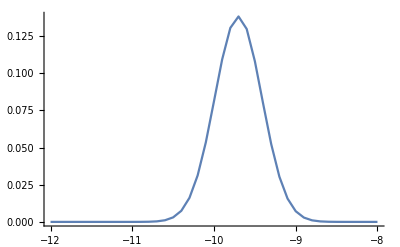

```mathematica
ListLinePlot[Transpose[{mu0Range,mu0Table}],PlotRange->{Automatic,Full}]
```

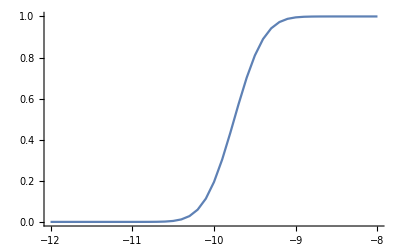

```mathematica
ListLinePlot[Transpose[{mu0Range,mu0TrueCDF}],PlotRange->{Automatic,Full}]
```

```mathematica
matrix = Table[0,{r,Length[mu0Range]},{c, Length[epslist]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[i = 1, i <= Length[epslist], i++,
 e = epslist[[i]];
mu0TableEps = Table[NIntegrate[plu[theta, mu0, mu1,e], {theta,0,1}, {mu1,5,15}],{mu0, mu0Range}];
 mu0normEps = Total[mu0TableEps];
mu0TableEps = mu0TableEps/mu0normEps;
mu0CDFEps = Table[Function[upto,Sum[mu0TableEps[[i]], {i, 1,upto}]][i], {i,1, Length[mu0TableEps]}];
matrix[[All,i]] = mu0CDFEps;
 ]
```

```mathematica
KS = Table[Max[Abs[matrix[[All, i]] - mu0TrueCDF]],{i,1,Length[epslist]}]
```

{0.0962871,0.0857743,0.0763628,0.0679169,0.0603186,0.0534654,0.0472686,0.0416518,0.0366433,0.0320569,0.0278497,0.0239833,0.0204237,0.017141,0.0141083,0.0113019,0.00870072,0.00628587,0.00404056,0.00194976,0.,0.00182079,0.00352345,0.00511775,0.00661249,0.00801562,0.00933432,0.0105751,0.0117439,0.012846,0.0138864,0.0148696,0.0157994,0.0166798,0.0175141,0.0183055,0.0190567,0.0197704,0.0204491,0.0210949,0.02171}

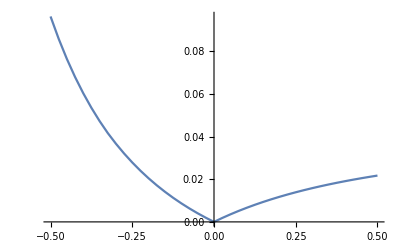

```mathematica
ListLinePlot[Transpose[{epslist,KS}],PlotRange->{Automatic,Full}]
```

```mathematica
Export[NotebookDirectory[]<>"normal_mixture_mu[0]_2.csv",{epslist,mu0Range,matrix, KS}]
```

/home/ez/sense/benchmarks/stan_bench/normal_mixture/normal_mixture_mu[0]_2.csv